```mathematica
normKMod[V_,kappa_]:=1/π^(3/2)(kappa^(3/2)/2 Gamma[kappa-1/2]/Gamma[kappa+1]+V/π^(1/2)Hypergeometric2F1[1/2,kappa,3/2,-V^2/kappa])^-1
barbKappaMod[vpar_,vperp_,V_,alpha_,kappa_]:=normKMod[V,kappa] (1+(vpar^2+vperp^2+V^2-2 V(vpar^2+vperp^2(1-alpha))^(1/2))/kappa)^(-(kappa+1))UnitStep[vpar]
```

```mathematica
barb[α_,vOvera_]:=1+(2(1-α)vOvera Exp[-α vOvera^2])/Erfc[-vOvera] NIntegrate[Exp[α x^2]Erfc[x],{x,-vOvera,∞}]
barbK[alpha_,vOvera_,kappa_]:=NIntegrate[2 π vperp barbKappaMod[vpar,vperp,vOvera,alpha,kappa],{vpar,0,∞},{vperp,0,∞}]
```

### vOvera=5 case

```mathematica
alphaList=PowerRange[0.000001,1,1.5];
```

```mathematica
vOvera=5;
```

```mathematica
Table[{1/alpha,barbK[alpha,vOvera,2]},{alpha,alphaList}]
```

{{1.×10^6,38.6666},{666667.,38.6662},{444444.,38.6656},{296296.,38.6647},{197531.,38.6633},{131687.,38.6612},{87791.5,38.6581},{58527.7,38.6534},{39018.4,38.6464},{26012.3,38.6359},{17341.5,38.6201},{11561.,38.5964},{7707.35,38.561},{5138.23,38.508},{3425.49,38.4286},{2283.66,38.3101},{1522.44,38.1335},{1014.96,37.8711},{676.639,37.4831},{451.093,36.9133},{300.729,36.0852},{200.486,34.8998},{133.657,33.2393},{89.1048,30.9843},{59.4032,28.0501},{39.6021,24.4449},{26.4014,20.3281},{17.6009,16.0243},{11.734,11.9487},{7.82264,8.46221},{5.2151,5.74858},{3.47673,3.79568},{2.31782,2.46804},{1.54521,1.59639},{1.03014,1.03269}}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

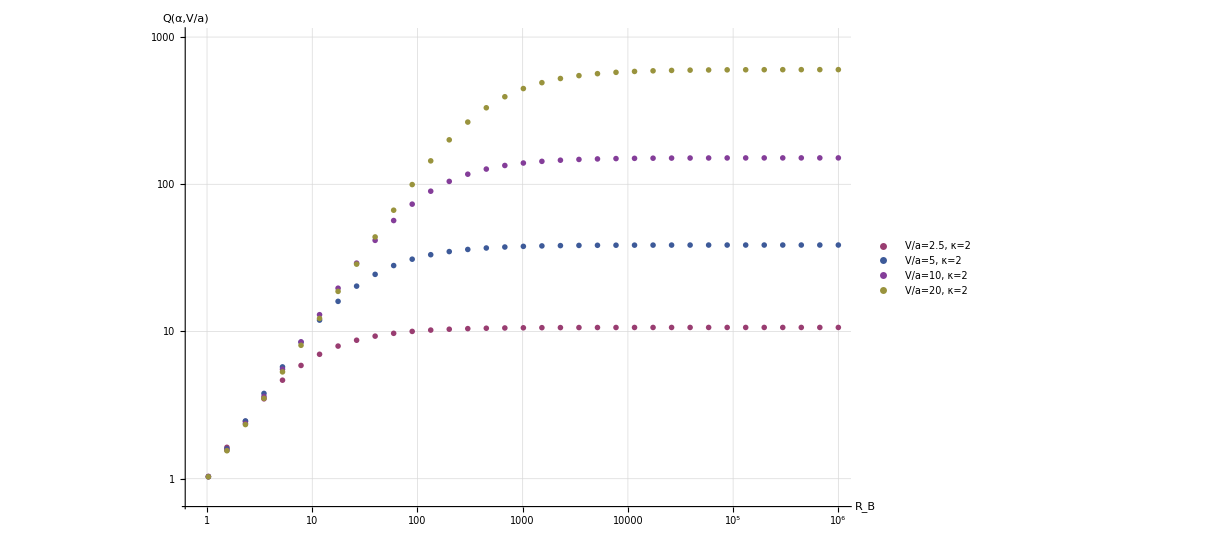

```mathematica
Show[Table[ListLogLogPlot[Legended[Table[{1/alpha,barbK[alpha,vOvera,2]},{alpha,alphaList}],StringForm["V/a=`1`, κ=`2`",NumberForm[vOvera,2],2]],PlotStyle->ColorData[1][vOvera],PlotRange->{All,1*^3},PlotMarkers-> {Automatic,Medium},PlotLegends->LineLegend[Automatic,LegendMarkerSize->{{50,50}}],GridLines->Automatic,AxesLabel->{"R_B",StringForm["Q(α,V/a)"]},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->16],ImageSize->900],{vOvera,{2.5,5,10,20}}]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

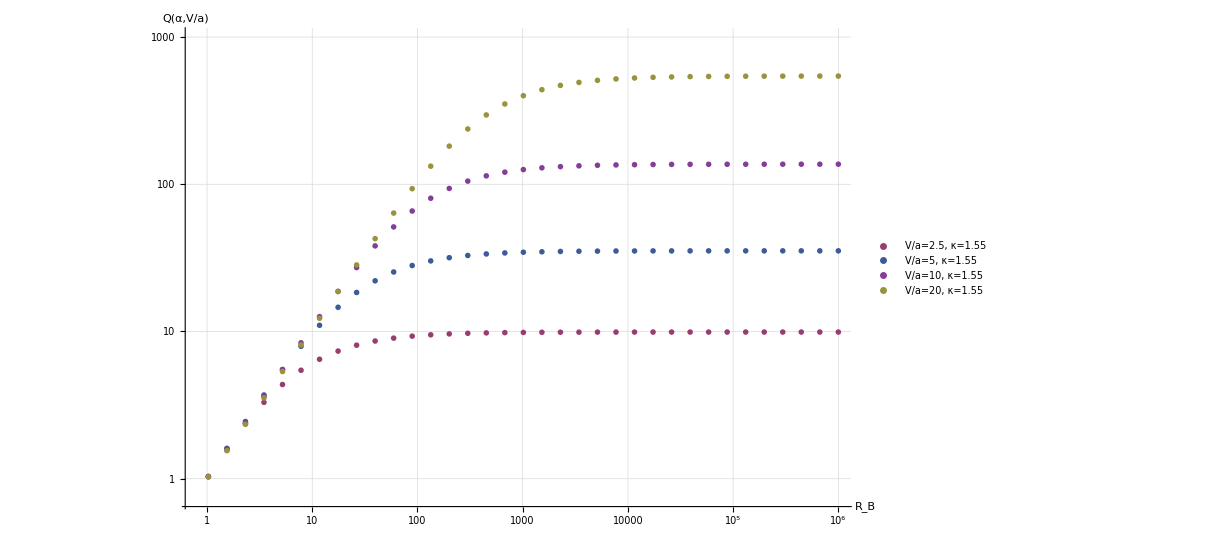

```mathematica
Show[Table[ListLogLogPlot[Legended[Table[{1/alpha,barbK[alpha,vOvera,1.55]},{alpha,alphaList}],StringForm["V/a=`1`, κ=`2`",NumberForm[vOvera,2],1.55]],PlotStyle->ColorData[1][vOvera],PlotRange->{All,1*^3},PlotMarkers-> {Automatic,Medium},PlotLegends->LineLegend[Automatic,LegendMarkerSize->{{50,50}}],GridLines->Automatic,AxesLabel->{"R_B",StringForm["Q(α,V/a)"]},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->16],ImageSize->900],{vOvera,{2.5,5,10,20}}]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

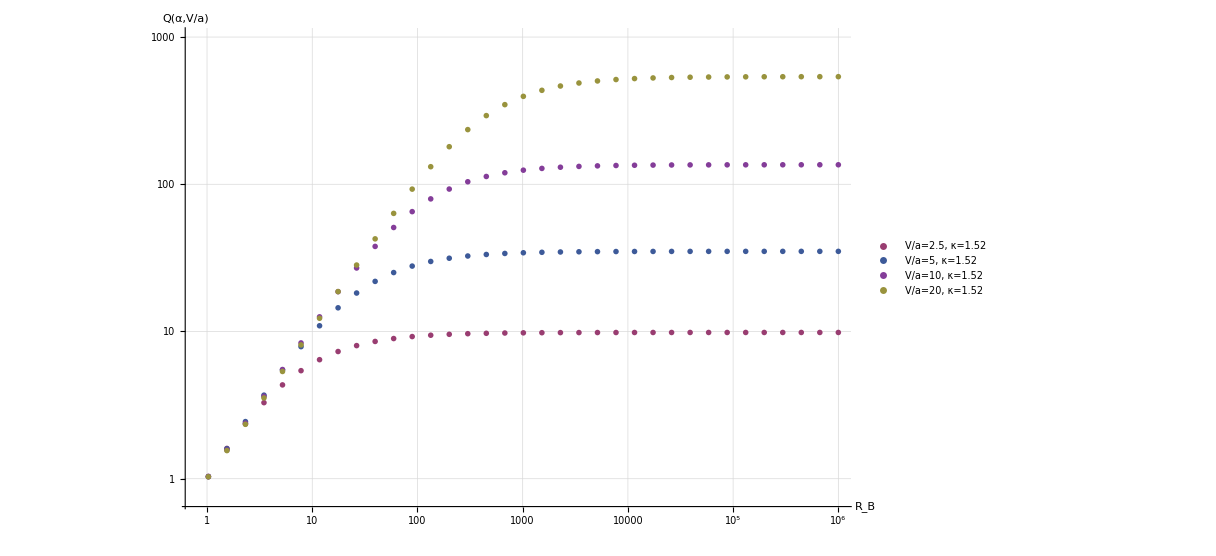

```mathematica
Show[Table[ListLogLogPlot[Legended[Table[{1/alpha,barbK[alpha,vOvera,1.52]},{alpha,alphaList}],StringForm["V/a=`1`, κ=`2`",NumberForm[vOvera,2],1.52]],PlotStyle->ColorData[1][vOvera],PlotRange->{All,1*^3},PlotMarkers-> {Automatic,Medium},PlotLegends->LineLegend[Automatic,LegendMarkerSize->{{50,50}}],GridLines->Automatic,AxesLabel->{"R_B",StringForm["Q(α,V/a)"]},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->16],ImageSize->900],{vOvera,{2.5,5,10,20}}]]
```